```mathematica
m=4
ParametricPlot3D[{(ρ+m)*Cos[ϕ],(ρ+m)*Sin[ϕ],ρ^2},{ρ,0,m/2},{ϕ,0,2π}]
```

4

8.854×10^-12

8.98774×10^9

17.556

{8.98774×10^9 (-(5.966×10^-13 (0.04-x))/(((0.04-x)^2+(0.07-y)^2)^(3/2))+(1.0359×10^-12 (0.037-x))/(((0.037-x)^2+(0.076-y)^2)^(3/2))),8.98774×10^9 (-(5.966×10^-13 (0.07-y))/(((0.04-x)^2+(0.07-y)^2)^(3/2))+(1.0359×10^-12 (0.076-y))/(((0.037-x)^2+(0.076-y)^2)^(3/2)))}

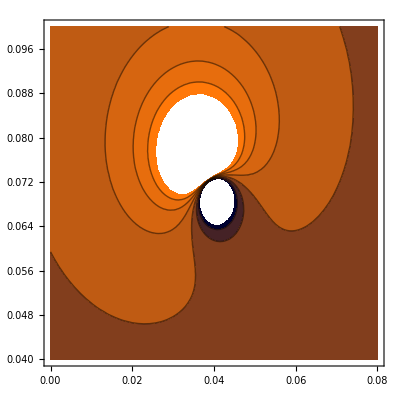

```mathematica
ϵ0= (8.854*10^-12)
k1=1/(4π*ϵ0)
q1 = -5.966*10^-13;
q2=1.0359*10^-12;
C1=17.556
V[x_,y_]:=k1*(q1/(√((0.04-x)^2+(0.07-y)^2))+q2/(√((0.037-x)^2+(0.076-y)^2)))
Grad[Evaluate@V[x,y],{x,y}]
ContourPlot[Evaluate@V[x,y],{x,0,0.08},{y,0.04,0.1},ColorFunction->ColorData["RustTones"]]
```

```mathematica
Integrate[(ρ/ρ0+1)*√(1+4(ρ/ρ0)^2),ρ]
```

1/12 √(1+4 ρ^2) (1+4 ρ^2+6 ρ ρ0)-1/4 ρ0 Log[-2 ρ+√(1+4 ρ^2)]

```mathematica
A[ρ_]:=1/12 √(1+4 ρ^2) (1+4 ρ^2+6 ρ ρ0)-1/4 ρ0 Log[-2 ρ+√(1+4 ρ^2)]
```

```mathematica
FullSimplify[A[ρ1]-A[ρ0]]
```

1/12 (-√(1+4 ρ0^2) (1+10 ρ0^2)+√(1+4 ρ1^2) (1+6 ρ0 ρ1+4 ρ1^2)-3 ρ0 ArcSinh[2 ρ0]+3 ρ0 ArcSinh[2 ρ1])